# Industrial Robotics - Exam 01/02/2016

```mathematica
ClearAll[“Global`*”]
```

-Graphics-
 The 3 degrees of freedom robot in the picture is composed of a revolute joint and two prismatic
joints. The rotation q1 is performed about axis z0, the translation q2 along axis x1 (only negative)
and the translation q3 (only positive) along axis z2. When q1=0 axes x0 and x1 are aligned, when
q2=0 axes z1 and z2 are aligned and opposed, when q3=0 axes x2 and x3 overlap.

### 1) Find the Jacobian matrix . Find and explain the singular configurations.

```mathematica
MrotZtrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
```

Focus on RF1:

```mathematica
O1={L1 Cos[q1[t]],L1 Sin[q1[t]],L1,1};
M01=MrotZtrasl[q1[t],O1];
M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | L1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | L1 Sin[q1[t]]
0 | 0 | 1 | L1
0 | 0 | 0 | 1)

Focus on RF2:

```mathematica
O2rf1={q2[t],0,-L2,1};
M12p=MrotZtrasl[0,O2rf1];
(*x2=y2p;y2=x2p;z2=-z2p*)
M2p2=Transpose[{{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,1}}];
M12=M12p.M2p2;
M02=M01.M12;
M02//MatrixForm
```

(-Sin[q1[t]] | Cos[q1[t]] | 0 | L1 Cos[q1[t]]+Cos[q1[t]] q2[t]
Cos[q1[t]] | Sin[q1[t]] | 0 | L1 Sin[q1[t]]+q2[t] Sin[q1[t]]
0 | 0 | -1 | L1-L2
0 | 0 | 0 | 1)

Focus on RF3:

```mathematica
O3rf2={0,0,q3[t],1};
M23=MrotZtrasl[0,O3rf2];
M03=Simplify[M02.M23];
M03//MatrixForm
```

(-Sin[q1[t]] | Cos[q1[t]] | 0 | Cos[q1[t]] (L1+q2[t])
Cos[q1[t]] | Sin[q1[t]] | 0 | (L1+q2[t]) Sin[q1[t]]
0 | 0 | -1 | L1-L2-q3[t]
0 | 0 | 0 | 1)

Jacobian

```mathematica
EE=M03[[1;;3,4]];
Jac=Simplify[D[EE,{{q1[t],q2[t],q3[t]}}]];
Jac//MatrixForm
```

(-((L1+q2[t]) Sin[q1[t]]) | Cos[q1[t]] | 0
Cos[q1[t]] (L1+q2[t]) | Sin[q1[t]] | 0
0 | 0 | -1)

Singular Configurations

```mathematica
detJac=Simplify[Det[Jac]]
```

L1+q2[t]

```mathematica
q2Singular=Solve[detJac==0,q2[t]]
```

{{q2[t]→-L1}}

When , the EE is aligned with axis z0.
In this singular configuration, the Jacobian rank drops to 2. 
The robot loses the ability to generate velocity in the tangential direction (rotation of  produces no displacement). 
However, it retains two degrees of freedom: it can still translate vertically (along ) and extend radially (along the direction of the arm).

### 2) The end effector must be moved with zero initial and final velocity from joint configuration (π / 4, -0.5, 0.3) to (-π / 4, 0, 0.1) with constant acceleration profiles.The maximum accelerations at the joints are (2 rad / s2, 2 m / s2, 3 m / s2): find the overall minimum time and rescale the accelerations in order to synchronize the joints.

```mathematica
solTmin=T/.Solve[Δq==2 1/2 aMax (T/2)^2,T]
```

{-(2 √Δq)/(√aMax),(2 √Δq)/(√aMax)}

```mathematica
Tmin[Δq_,aMax_]:=2 √(Abs[Δq]/aMax)
aMaxData={aMaxNum1->2,aMaxNum2->2,aMaxNum3->3};
q1i=π/4;q2i=-0.5;q3i=0.3;
q1f=-π/4;q2f=0;q3f=0.1;
```

Find traveling time of every joint.

```mathematica
Tt1=Tmin[q1f-q1i,aMaxNum1]/.aMaxData//N
```

1.77245

```mathematica
Tt2=Tmin[q2f-q2i,aMaxNum2]/.aMaxData//N
```

1.

```mathematica
Tt3=Tmin[q3f-q3i,aMaxNum3]/.aMaxData//N
```

0.516398

Find minimum time.

```mathematica
Tf=Max[Tt1,Tt2,Tt3]
```

1.77245

Rescale the accelerations.

```mathematica
amaxRescaled=Solve[Δq==2 1/2 aMax (Tt/2)^2,aMax]
```

{{aMax→(4 Δq)/Tt^2}}

```mathematica
aMaxFormula[Δq_,Tt_]:=(4 Δq)/Tt^2
```

```mathematica
aMax1Rescaled=aMaxFormula[q1f-q1i,Tf]
```

-2.

```mathematica
aMax2Rescaled=aMaxFormula[q2f-q2i,Tf]
```

0.63662

```mathematica
aMax3Rescaled=aMaxFormula[q3f-q3i,Tf]
```

-0.254648

Define the triangular profiles.

```mathematica
baseProfile=Piecewise[{{qin+1/2 a t^2,0<=t<=T/2},{qin+a T^2/4-((T-t)^2 a)/2,T/2<t<=T}}]
```

Piecewise[{{qin+(a t^2)/2, 0≤t≤T/2}, {qin+(a T^2)/4-1/2 a (-t+T)^2, T/2<t≤T}, {0, True}}]

```mathematica
q1Profile=baseProfile/.a->aMax1Rescaled/.qin->q1i/.T->Tf
```

Piecewise[{{π/4-1. t^2, 0≤t≤0.886227}, {-0.785398+1. (1.77245-t)^2, 0.886227<t≤1.77245}, {0, True}}]

```mathematica
q2Profile=baseProfile/.a->aMax2Rescaled/.qin->q2i/.T->Tf
```

Piecewise[{{-0.5+0.31831 t^2, 0≤t≤0.886227}, {0.-0.31831 (1.77245-t)^2, 0.886227<t≤1.77245}, {0, True}}]

```mathematica
q3Profile=baseProfile/.a->aMax3Rescaled/.qin->q3i/.T->Tf
```

Piecewise[{{0.3-0.127324 t^2, 0≤t≤0.886227}, {0.1+0.127324 (1.77245-t)^2, 0.886227<t≤1.77245}, {0, True}}]

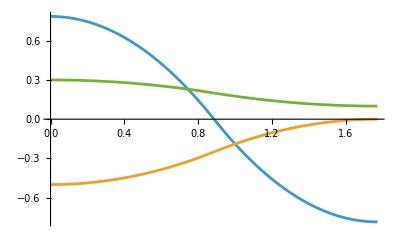

```mathematica
Plot[{q1Profile,q2Profile,q3Profile},{t,0,Tf}]
```

### 3) Assume: Link 1 can be considered a lumped mass located in G1=(-3/4*L1, 0, -1/4*L1) Link 2 can be considered a lumped mass located in G2=(0, 0, -1/2*L2) Link 3 can be considered a lumped mass located in G3=E Link 1 is subjected to a viscous force F along -y1 applied to the point (-1/3*L1, 0, 0) The gravity force can be neglected. Find the symbolic equations of motion of the robot in the presence of a proportional controller on each axis.

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];
W02=Simplify[D[M02,t].Inverse[M02]];
W03=Simplify[D[M03,t].Inverse[M03]];
```

```mathematica
J11={{m1(-3/4 L1)^2,0,m1(-3/4 L1)(-1/4 L1),m1(-3/4 L1)},{0,0,0,0},{m1(-1/4 L1)(-3/4 L1),0,m1(-1/4 L1)^2,m1(-1/4 L1)},{m1(-3/4 L1),0,m1(-1/4 L1),m1}};
J11//MatrixForm
```

((9 L1^2 m1)/16 | 0 | (3 L1^2 m1)/16 | -(3 L1 m1)/4
0 | 0 | 0 | 0
(3 L1^2 m1)/16 | 0 | (L1^2 m1)/16 | -(L1 m1)/4
-(3 L1 m1)/4 | 0 | -(L1 m1)/4 | m1)

```mathematica
J22={{0,0,0,0},{0,0,0,0},{0,0,m2(-1/2 L2)^2,m2(-1/4 L2)},{0,0,m2(-1/2 L2),m2}};
J22//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (L2^2 m2)/4 | -(L2 m2)/4
0 | 0 | -(L2 m2)/2 | m2)

```mathematica
J33={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,m3}};
J33//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | m3)

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];
J20=Simplify[M02.J22.Transpose[M02]];
J30=Simplify[M03.J33.Transpose[M03]];
```

```mathematica
T1=Simplify[1/2 Tr[W01.J10.Transpose[W01]]];
T2=Simplify[1/2 Tr[W02.J20.Transpose[W02]]];
T3=Simplify[1/2 Tr[W03.J30.Transpose[W03]]];
```

Non-Lagrangian components.

```mathematica
cx=0;cy=0;cz=1/3 L1 Fvisc;
fx=0;fy=-Fvisc;fz=0;
Phi11={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
Phi11//MatrixForm
```

(0 | -(Fvisc L1)/3 | 0 | 0
(Fvisc L1)/3 | 0 | 0 | -Fvisc
0 | 0 | 0 | 0
0 | Fvisc | 0 | 0)

```mathematica
Phi10=Simplify[M01.Phi11.Transpose[M01]];
Phi10//MatrixForm
```

(0 | (2 Fvisc L1)/3 | Fvisc L1 Sin[q1[t]] | Fvisc Sin[q1[t]]
-(2 Fvisc L1)/3 | 0 | -Fvisc L1 Cos[q1[t]] | -Fvisc Cos[q1[t]]
-Fvisc L1 Sin[q1[t]] | Fvisc L1 Cos[q1[t]] | 0 | 0
-Fvisc Sin[q1[t]] | Fvisc Cos[q1[t]] | 0 | 0)

```mathematica
(*Function to compute the Pseudo Scalar Product*)
PSP[Mat1_,Mat2_]:=Mat1⟦3,2⟧*Mat2⟦3,2⟧+Mat1⟦1,3⟧*Mat2⟦1,3⟧+Mat1⟦2,1⟧*Mat2⟦2,1⟧+Mat1⟦1,4⟧*Mat2⟦1,4⟧+Mat1⟦2,4⟧*Mat2⟦2,4⟧+Mat1⟦3,4⟧*Mat2⟦3,4⟧;
```

```mathematica
L01=W01/q1'[t]
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Q1=Simplify[PSP[Phi10,L01]]
```

-(2 Fvisc L1)/3

It is possible to find the Lagrangian term.

```mathematica
Lagr=FullSimplify[T1+T2+T3]
```

1/32 ((L1^2 (m1+16 (m2+m3))+16 (m2+m3) q2[t] (2 L1+q2[t])) q1'[t]^2+16 ((m2+m3) q2'[t]^2+m3 q3'[t]^2))

Equation 1:

```mathematica
dLagrdq1dotdt=Simplify[D[D[Lagr,q1'[t]],t]]
```

2 (m2+m3) (L1+q2[t]) q1'[t] q2'[t]+1/16 (L1^2 (m1+16 (m2+m3))+32 L1 (m2+m3) q2[t]+16 (m2+m3) q2[t]^2) q1''[t]

```mathematica
dLagrdq1=Simplify[D[Lagr,q1[t]]]
```

0

Equation 2:

```mathematica
dLagrdq2dotdt=Simplify[D[D[Lagr,q2'[t]],t]]
```

(m2+m3) q2''[t]

```mathematica
dLagrdq2=Simplify[D[Lagr,q2[t]]]
```

(m2+m3) (L1+q2[t]) q1'[t]^2

Equation 3:

```mathematica
dLagrdq3dotdt=Simplify[D[D[Lagr,q3'[t]],t]]
```

m3 q3''[t]

```mathematica
dLagrdq3=Simplify[D[Lagr,q3[t]]]
```

0

Equations of Motion

```mathematica
equation1=dLagrdq1dotdt-dLagrdq1-C1-Q1 //Simplify
```

-C1+(2 Fvisc L1)/3+2 (m2+m3) (L1+q2[t]) q1'[t] q2'[t]+1/16 (L1^2 (m1+16 (m2+m3))+32 L1 (m2+m3) q2[t]+16 (m2+m3) q2[t]^2) q1''[t]

```mathematica
equation2=dLagrdq2dotdt-dLagrdq2-F2//Simplify
```

-F2-(m2+m3) (L1+q2[t]) q1'[t]^2+(m2+m3) q2''[t]

```mathematica
equation3=dLagrdq3dotdt-dLagrdq3-F3//Simplify
```

-F3+m3 q3''[t]

Controllers

```mathematica
C1control=kp1 (q1d[t]-q1[t])
```

kp1 (-q1[t]+q1d[t])

```mathematica
F2control=kp2 (q2d[t]-q2[t])
```

kp2 (-q2[t]+q2d[t])

```mathematica
F3control=kp3 (q3d[t]-q3[t])
```

kp3 (-q3[t]+q3d[t])

Equations of Motion with Control Equations

```mathematica
eqControl1=equation1/.C1->C1control//Simplify
```

(2 Fvisc L1)/3+kp1 (q1[t]-q1d[t])+2 (m2+m3) (L1+q2[t]) q1'[t] q2'[t]+1/16 (L1^2 (m1+16 (m2+m3))+32 L1 (m2+m3) q2[t]+16 (m2+m3) q2[t]^2) q1''[t]

```mathematica
eqControl2=equation2/.F2->F2control//Simplify
```

kp2 (q2[t]-q2d[t])-(m2+m3) (L1+q2[t]) q1'[t]^2+(m2+m3) q2''[t]

```mathematica
eqControl3=equation3/.F3->F3control//Simplify
```

kp3 q3[t]-kp3 q3d[t]+m3 q3''[t]

### 4) Assuming L1 = 1 m, L2 = 0.5 m, m1 = 20 kg, m2 = 5 kg, m3 = 3 kg, the gains of the proportional controllers k1 = 1000, k2 = 1000, k3 = 1000, find the resulting joint motion profiles when the robot is commanded to follow the rescaled profiles of point 2.

```mathematica
lenData={L1->1,L2->0.5};
massData={m1->20,m2->5,m3->3};
kpData={kp1->1000,kp2->1000,kp3->1000};
allData=Join[lenData,massData,kpData];
```

Find Real Joint History

```mathematica
eq1CtrlNum=eqControl1/.allData/.q1d[t]->q1Profile/.Fvisc->2q1'[t]
```

1000 (-(Piecewise[{{π/4-1. t^2, 0≤t≤0.886227}, {-0.785398+1. (1.77245-t)^2, 0.886227<t≤1.77245}, {0, True}}])+q1[t])+(4 q1'[t])/3+16 (1+q2[t]) q1'[t] q2'[t]+1/16 (148+256 q2[t]+128 q2[t]^2) q1''[t]

```mathematica
eq2CtrlNum=eqControl2/.allData/.q2d[t]->q2Profile
```

1000 (-(Piecewise[{{-0.5+0.31831 t^2, 0≤t≤0.886227}, {0.-0.31831 (1.77245-t)^2, 0.886227<t≤1.77245}, {0, True}}])+q2[t])-8 (1+q2[t]) q1'[t]^2+8 q2''[t]

```mathematica
eq3CtrlNum=eqControl3/.allData/.q3d[t]->q3Profile
```

-1000 (Piecewise[{{0.3-0.127324 t^2, 0≤t≤0.886227}, {0.1+0.127324 (1.77245-t)^2, 0.886227<t≤1.77245}, {0, True}}])+1000 q3[t]+3 q3''[t]

```mathematica
closedLoopSol=Flatten@NDSolve[{eq1CtrlNum==0,eq2CtrlNum==0,eq3CtrlNum==0,
q1[0]==q1i,q1'[0]==0,q2[0]==q2i,q2'[0]==0,q3[0]==q3i,q3'[0]==0},
{q1[t],q2[t],q3[t]},{t,0,Tf}]
```

{q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t],q3[t]→InterpolatingFunction[…][t]}

Plot Profiles

```mathematica
q1t=q1[t]/.closedLoopSol;
q2t=q2[t]/.closedLoopSol;
q3t=q3[t]/.closedLoopSol;
```

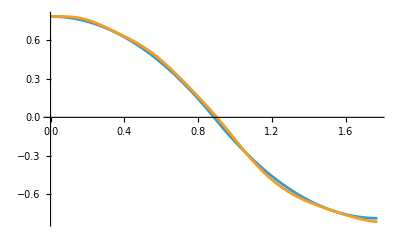

```mathematica
Plot[{q1Profile,q1t},{t,0,Tf}]
```

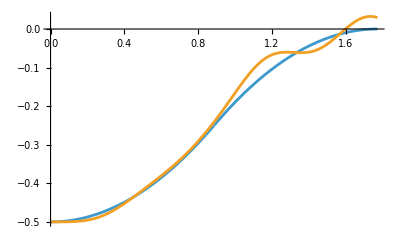

```mathematica
Plot[{q2Profile,q2t},{t,0,Tf}]
```

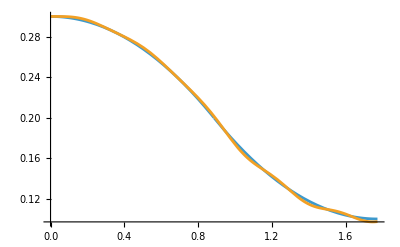

```mathematica
Plot[{q3Profile,q3t},{t,0,Tf}]
```

```mathematica
(*check for t=1*)
{q1t,q2t,q3t}/.t->1
```

{-0.171601,-0.165942,0.173833}

### Optional: plot the torques and force exerted by the motor in the closed loop configuration.

```mathematica
C1closedLoop=C1control/.allData/.q1d[t]->q1Profile/.q1[t]->q1t/.Fvisc->2q1'[t];
F2closedLoop=F2control/.allData/.q2d[t]->q2Profile/.q2[t]->q2t;
F3closedLoop=F3control/.allData/.q3d[t]->q3Profile/.q3[t]->q3t;
```

Plot Torques (& Forces) in Losed Loop

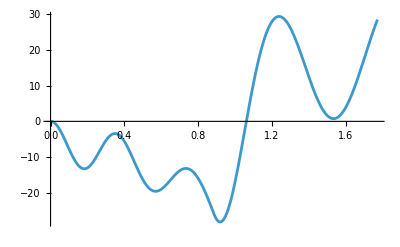

```mathematica
Plot[C1closedLoop,{t,0,Tf}]
```

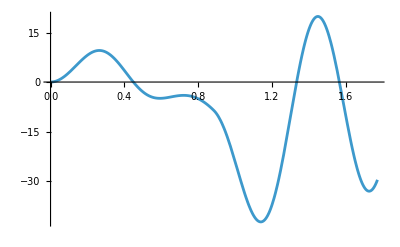

```mathematica
Plot[F2closedLoop,{t,0,Tf}]
```

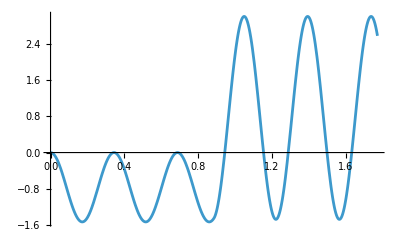

```mathematica
Plot[F3closedLoop,{t,0,Tf}]
```

### Optional: find the torque & forces in open-loop inverse dynamics.

```mathematica
C1InvDyn=C1/.Flatten[Solve[equation1==0,C1]];
F2InvDyn=F2/.Flatten[Solve[equation2==0,F2]];
F3InvDyn=F3/.Flatten[Solve[equation3==0,F3]];
```

```mathematica
C1InvDynNum=C1InvDyn/.allData/.Fvisc->2q1'[t]/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t];
F2InvDynNum=F2InvDyn/.allData/.q2[t]->q2Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t];
F3InvDynNum=F3InvDyn/.allData/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t];
```

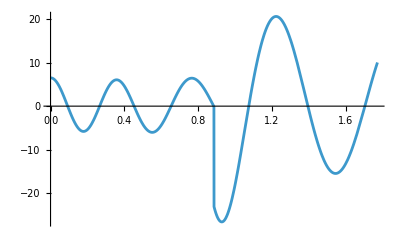

```mathematica
Plot[C1closedLoop-C1InvDynNum,{t,0,Tf}]
```

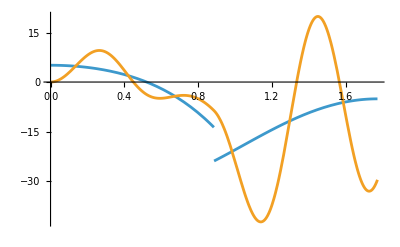

```mathematica
Plot[{F2InvDynNum,F2closedLoop},{t,0,Tf}]
```

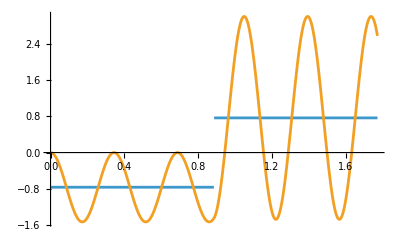

```mathematica
Plot[{F3InvDynNum,F3closedLoop},{t,0,Tf}]
```